```mathematica
SetDirectory["C:\\Users\\Lion\\Documents\\My Projects\\GOT"]
```

C:\Users\Lion\Documents\My Projects\GOT

```mathematica
FileNames[]
```

{1.png,C.png,Cp.png,D.png,Dp.png,Extract txt,Fighting.png,Fights.txt,game-of-thrones-tokens.png,houseB.gif,houseG.gif,houseL.gif,houseM.gif,houseS.gif,Houses.PNG,houseT.gif,.ipynb_checkpoints,Mm.png,M.png,Mp.png,Node,OpeningMovesBara.png,OpeningMoves.nb,OpeningMoves.png,Results,R.png,Rp.png,S.png,Sp.png,Stark.png,test.png,Tokens.png,Tokens.xcf,Untitled.ipynb}

```mathematica
HousesImages=<|"Tyrell"->Import["houseT.gif"],"Lannister"->Import["houseL.gif"],"Greyjoy"->Import["houseG.gif"],"Martell"->Import["houseM.gif"],"Stark"->Import["houses.gif"],"Baratheon"->Import["houseB.gif"]|>
```

<|Tyrell→-Graphics-,Lannister→-Graphics-,Greyjoy→-Graphics-,Martell→-Graphics-,Stark→-Graphics-,Baratheon→-Graphics-|>

```mathematica
"Tyrell"/.HousesImages
```

-Graphics-

```mathematica
SetDirectory["C:\\Users\\Lion\\Documents\\My Projects\\GOT\\Extract txt\\Fights"]
```

C:\Users\Lion\Documents\My Projects\GOT\Extract txt\Fights

```mathematica
FileNames[]
```

{Fights.txt,test.png}

```mathematica
fights=Import["Fights.txt","Table","FieldSeparators"->","];
```

```mathematica
Print["Occupied Memory:",NumberForm[ByteCount[fights]*10.^-6,2]," Mb"]
```

Occupied Memory:83. Mb

```mathematica
nrfights=Transpose[fights][[1]];
nrs=DeleteDuplicates[Transpose[fights][[1]]];
```

```mathematica
Length[nrs]
```

7876

#### Number of fights:

```mathematica
Monitor[fightnumber=Table[{nrs[[i]],Count[nrfights,nrs[[i]]]},{i,1,Length[nrs]}];,i]
```

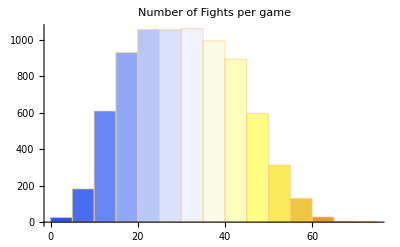

```mathematica
histdata=Transpose[fightnumber][[2]];
Histogram[histdata,20,ChartStyle->"Temperature",PlotLabel->"Number of Fights per game"]
```

Get the one with the largest number of fights:

```mathematica
largest=TakeLargest[Transpose[fightnumber][[2]],1][[1]];
smallest=TakeSmallest[Transpose[fightnumber][[2]],1][[1]];
maxpos=Position[Transpose[fightnumber][[2]],largest][[1,1]];
minpos=Position[Transpose[fightnumber][[2]],smallest][[1,1]];
fightnumber[[maxpos]]
fightnumber[[minpos]]
```

{140390,73}

{95816,2}

#### Fight between houses

```mathematica
houses={"Lannister","Greyjoy","Baratheon","Martell","Tyrell","Stark"}
```

{Lannister,Greyjoy,Baratheon,Martell,Tyrell,Stark}

```mathematica
pairings=Permutations[houses,{2}];
statistics=Table[{pairings[[i]],Count[fights,Flatten[{_,{pairings[[i]]},_,_}]]},{i,1,Length[pairings]}];
a=Transpose[statistics][[2]];
a=ArrayReshape[a,{6,5}];
b=Table[Insert[a[[i]],0,i],{i,1,Length[a]}];
```

```mathematica
tikc1=Map[HousesImages,houses];
htick={#,tikc1[[#]]}&/@Range[Length[tikc1]];
arr=ArrayPlot[b,FrameTicks->{htick,htick},RotateLabel->True,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->{100,1550}],Right],FrameLabel->{"Attacker","Defender"},RotateLabel->True,PlotLabel->StringForm["Total number of attacks. From `` games",Length[nrs]],ColorFunction->(ColorData["Temperature"][Rescale[#1,{-TakeLargest[Flatten[b],1][[1]],TakeLargest[Flatten[b],1][[1]]}]]&),ColorFunctionScaling->False,ImageSize->Full,LabelStyle->FontSize->50];
Export["test.png",arr];
ImageResize[Import["test.png"],500]
```

-Graphics-

Now lets do it in average per game.

```mathematica
splitted=SplitBy[fights,First];
Length[splitted]
```

7876

```mathematica
GL=Table[{splitted[[i,1,1]],Count[splitted[[i]], Flatten[{_, "Lannister", "Greyjoy", _, _}]] + Count[splitted[[i]], Flatten[{_, "Greyjoy", "Lannister", _, _}]]},{i,1,Length[splitted]}];
GS=Table[{splitted[[i,1,1]],Count[splitted[[i]], Flatten[{_, "Stark", "Greyjoy", _, _}]] + Count[splitted[[i]], Flatten[{_, "Greyjoy", "Stark", _, _}]]},{i,1,Length[splitted]}];
Gfights=Table[{splitted[[i,1,1]],Count[splitted[[i]], Flatten[{_, _, "Greyjoy", _, _}]] + Count[splitted[[i]], Flatten[{_, "Greyjoy", _, _, _}]]},{i,1,Length[splitted]}];
```

```mathematica
MT=Table[{splitted[[i,1,1]],Count[splitted[[i]], Flatten[{_, "Martell", "Tyrell", _, _}]] + Count[splitted[[i]], Flatten[{_, "Tyrell", "Martell", _, _}]]},{i,1,Length[splitted]}];
MB=Table[{splitted[[i,1,1]],Count[splitted[[i]], Flatten[{_, "Martell", "Baratheon", _, _}]] + Count[splitted[[i]], Flatten[{_, "Baratheon", "Martell", _, _}]]},{i,1,Length[splitted]}];
```

```mathematica
MT
```

{{90001,6},{90017,7},{90028,8},{90032,8},{90035,17},{90051,0},{90070,0},{90078,3},{90079,1},{90083,3},{90087,0},{90089,2},{90091,4},{90092,1},{90093,1},{90113,6},{90116,3},{90132,6},{90142,0},{90144,0},{90149,10},{90154,0},{90155,5},{90162,9},{90171,5},{90174,5},{90175,6},{90192,5},{90204,2},{90206,3},{90209,11},{90212,9},{90213,7},{90219,10},{90223,5},{90224,13},{90230,9},{90236,7},7800,{144452,10},{144455,4},{144468,4},{144470,2},{144473,9},{144478,5},{144497,4},{144501,14},{144507,1},{144527,6},{144532,0},{144555,6},{144560,5},{144566,0},{144571,4},{144588,2},{144596,1},{144599,7},{144611,6},{144614,1},{144616,0},{144627,1},{144673,2},{144677,0},{144679,6},{144685,5},{144695,13},{144698,1},{144705,2},{144714,0},{144717,8},{144736,1},{144753,9},{144772,0},{144778,6},{144780,9},{144783,5},{144808,5}}
 |  |  |  |

```mathematica
TL=Table[{splitted[[i,1,1]],Count[splitted[[i]], Flatten[{_, "Lannister", "Tyrell", _, _}]] + Count[splitted[[i]], Flatten[{_, "Tyrell", "Lannister", _, _}]]},{i,1,Length[splitted]}];
TG=Table[{splitted[[i,1,1]],Count[splitted[[i]], Flatten[{_, "Tyrell", "Greyjoy", _, _}]] +0*Count[splitted[[i]], Flatten[{_, "Greyjoy", "Tyrell", _, _}]]},{i,1,Length[splitted]}];
```

```mathematica
TG
```

{{90001,0},{90017,0},{90028,0},{90032,1},{90035,2},{90051,1},{90070,0},{90078,0},{90079,0},{90083,0},{90087,0},{90089,0},{90091,0},{90092,0},{90093,1},{90113,0},{90116,4},{90132,0},{90142,3},{90144,0},{90149,0},{90154,0},{90155,0},{90162,0},{90171,0},{90174,1},{90175,0},{90192,5},{90204,0},{90206,0},{90209,0},{90212,0},{90213,2},{90219,0},{90223,0},{90224,0},{90230,0},{90236,0},{90247,0},7799,{144452,1},{144455,0},{144468,0},{144470,1},{144473,0},{144478,0},{144497,2},{144501,6},{144507,0},{144527,0},{144532,0},{144555,0},{144560,0},{144566,0},{144571,1},{144588,1},{144596,2},{144599,0},{144611,4},{144614,5},{144616,0},{144627,0},{144673,0},{144677,0},{144679,0},{144685,0},{144695,2},{144698,0},{144705,2},{144714,3},{144717,1},{144736,0},{144753,0},{144772,0},{144778,0},{144780,0},{144783,3},{144808,0}}
 |  |  |  |

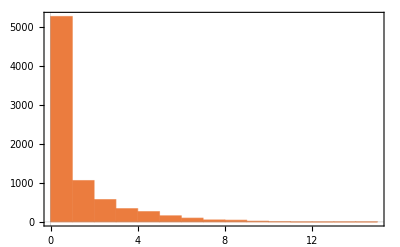

```mathematica
Histogram[Transpose[TG][[2]],PlotTheme->"Scientific",Frame->True]
```

```mathematica
ChartStyle
```

```mathematica
RGBColor[.9,.9,.9]
```

RGBColor[0.9, 0.9, 0.9]

```mathematica
Complement
```

```mathematica
Transpose[GL][[2]]
```

```mathematica
Orange+Green
```

RGBColor[0, 1, 0]+RGBColor[1, 0.5, 0]

```mathematica
RGBColor[1,0,1]
```

RGBColor[0, 0, 1]

```mathematica
Transpose[GL][[2]]//Length
```

7876

```mathematica
Transpose[GS][[2]]//Length
```

7876

{{5,5},{7,2},{5,2},{4,3},{4,11},{7,3},{4,0},{1,3},{4,2},{1,1},{4,5},{12,1},{10,6},{4,1},{5,3},{11,2},{8,2},{8,1},{4,4},{6,3},{9,10},{13,11},{9,0},{4,0},{4,2},{1,6},{7,8},{6,0},{5,3},{7,0},{1,14},{10,5},{11,14},{7,3},{9,7},{2,16},{8,10},{11,4},{13,4},{0,8},{5,14},{6,3},{7,3},{1,18},{5,2},{9,4},{8,2},{9,6},{3,6},{2,0},{2,9},{12,4},{4,13},{0,11},{7,12},{2,7},{7,2},{3,1},{3,3},{3,5},{1,5},{5,1},{8,0},{5,14},{11,1},{9,3},{0,6},{4,4},{4,1},{2,9},{4,4},{9,14},{12,1},7730,{0,9},{10,3},{2,17},{10,2},{12,3},{3,11},{6,4},{5,7},{7,0},{8,0},{6,3},{7,9},{9,0},{16,2},{0,3},{8,2},{8,1},{10,1},{6,1},{7,0},{7,4},{5,12},{3,11},{11,4},{6,9},{5,1},{8,3},{3,3},{6,7},{7,7},{5,1},{13,2},{10,3},{3,5},{3,3},{6,1},{5,3},{7,2},{0,5},{5,10},{5,1},{13,13},{10,7},{9,1},{4,6},{2,0},{4,2},{1,7},{3,0},{6,7},{4,9},{0,6},{1,3},{4,12},{8,1},{2,3},{0,4},{2,6},{5,1},{12,4},{7,10},{5,21},{5,2},{5,11},{5,1},{6,14},{2,8},{8,1},{8,1},{1,8},{13,1},{10,6},{0,5}}
 |  |  |  |

```mathematica
Histogram3D[Transpose[{Transpose[GL][[2]],Transpose[GS][[2]]}],AxesLabel->{"Fights vs Lannister","Fights vs Stark","#Games"},ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
GLSColor[{{xmin_,xmax_},{ymin_,ymax_}},___]:={RGBColor[.9,(-xmax+20)/30.,(-xmax+20)/30.],Rectangle[{xmin,ymin},{xmax,ymax}]};
MTBColor[{{xmin_,xmax_},{ymin_,ymax_}},___]:={If[xmax<0,RGBColor[(xmax+15.)/15.,.7+.3(xmax+15.)/(15.),(xmax+15.)/15.],RGBColor[1.,1,(-xmax+20)/20.]],Rectangle[{xmin,ymin},{xmax,ymax}]};
```

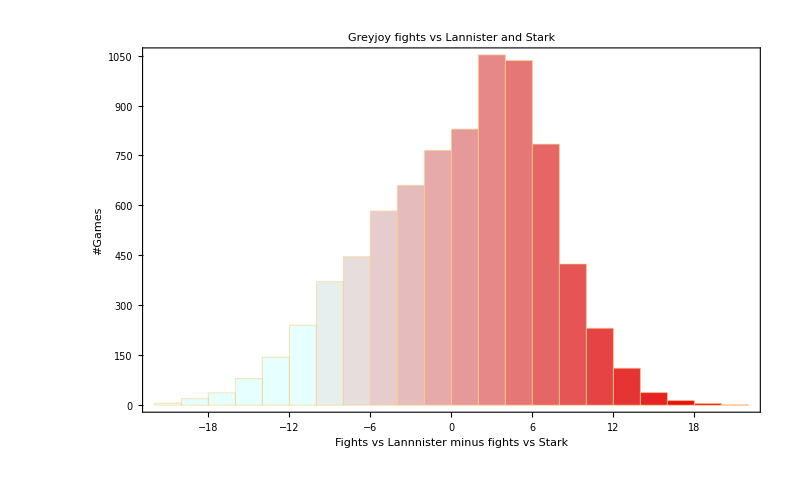

```mathematica
Histogram[Transpose[GL][[2]]-Transpose[GS][[2]],ChartElementFunction->GLSColor,Frame->True,FrameLabel->{"Fights vs Lannnister minus fights vs Stark","#Games"},PlotLabel->"Greyjoy fights vs Lannister and Stark"]
```

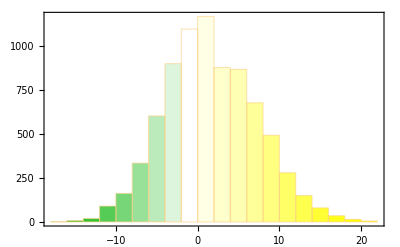

```mathematica
Histogram[Transpose[MT][[2]]-Transpose[MB][[2]],ChartElementFunction->MTBColor,Frame->True]
```

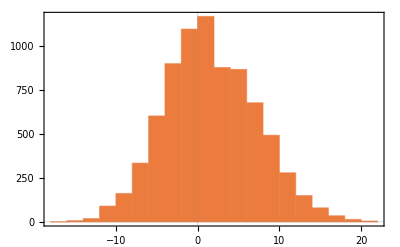

```mathematica
Histogram[Transpose[MT][[2]]-Transpose[MB][[2]],PlotTheme->"Scientific",Frame->True]
```

```mathematica
Transpose[GL][[1]]-Transpose[GS][[1]]
```

```mathematica
thresh=8
```

8

```mathematica
Clear[gsl]
```

```mathematica
fightsofGJ=Transpose[{Transpose[GL][[2]],Transpose[GS][[2]]}];
```

```mathematica
fightsofGJ
```

{{5,5},{7,2},{5,2},{4,3},{4,11},{7,3},{4,0},{1,3},{4,2},{1,1},{4,5},{12,1},{10,6},{4,1},{5,3},{11,2},{8,2},{8,1},{4,4},{6,3},{9,10},{13,11},{9,0},{4,0},{4,2},{1,6},{7,8},{6,0},{5,3},{7,0},{1,14},{10,5},{11,14},{7,3},{9,7},{2,16},{8,10},{11,4},{13,4},{0,8},{5,14},{6,3},{7,3},{1,18},{5,2},{9,4},{8,2},{9,6},{3,6},{2,0},{2,9},{12,4},{4,13},{0,11},{7,12},{2,7},{7,2},{3,1},{3,3},{3,5},{1,5},{5,1},{8,0},{5,14},{11,1},{9,3},{0,6},{4,4},{4,1},{2,9},{4,4},{9,14},{12,1},7730,{0,9},{10,3},{2,17},{10,2},{12,3},{3,11},{6,4},{5,7},{7,0},{8,0},{6,3},{7,9},{9,0},{16,2},{0,3},{8,2},{8,1},{10,1},{6,1},{7,0},{7,4},{5,12},{3,11},{11,4},{6,9},{5,1},{8,3},{3,3},{6,7},{7,7},{5,1},{13,2},{10,3},{3,5},{3,3},{6,1},{5,3},{7,2},{0,5},{5,10},{5,1},{13,13},{10,7},{9,1},{4,6},{2,0},{4,2},{1,7},{3,0},{6,7},{4,9},{0,6},{1,3},{4,12},{8,1},{2,3},{0,4},{2,6},{5,1},{12,4},{7,10},{5,21},{5,2},{5,11},{5,1},{6,14},{2,8},{8,1},{8,1},{1,8},{13,1},{10,6},{0,5}}
 |  |  |  |

```mathematica
MT
```

{{90001,6},{90017,7},{90028,8},{90032,8},{90035,17},{90051,0},{90070,0},{90078,3},{90079,1},{90083,3},{90087,0},{90089,2},{90091,4},{90092,1},{90093,1},{90113,6},{90116,3},{90132,6},{90142,0},{90144,0},{90149,10},{90154,0},{90155,5},{90162,9},{90171,5},{90174,5},{90175,6},{90192,5},{90204,2},{90206,3},{90209,11},{90212,9},{90213,7},{90219,10},{90223,5},{90224,13},{90230,9},{90236,7},7800,{144452,10},{144455,4},{144468,4},{144470,2},{144473,9},{144478,5},{144497,4},{144501,14},{144507,1},{144527,6},{144532,0},{144555,6},{144560,5},{144566,0},{144571,4},{144588,2},{144596,1},{144599,7},{144611,6},{144614,1},{144616,0},{144627,1},{144673,2},{144677,0},{144679,6},{144685,5},{144695,13},{144698,1},{144705,2},{144714,0},{144717,8},{144736,1},{144753,9},{144772,0},{144778,6},{144780,9},{144783,5},{144808,5}}
 |  |  |  |

```mathematica
TyrellvsGJ=Flatten[Transpose[TG][[1]][[#]]&/@(Flatten[Position[TG,{_Integer,_Integer?(#≥3&)}]])];
```

```mathematica
Cases[TyrellvsGJ,_Integer?(MemberQ[western,#]&)]
```

{90738,90820,90826,90954,91600,91740,92039,92475,93307,93355,93679,93784,94233,94914,95519,95674,96062,96491,96496,96701,96901,97227,97316,97679,97984,98087,98320,99873,100357,100815,101043,101055,101968,102181,102884,103307,103345,103348,103361,103522,103789,104048,104530,104777,105305,105444,105684,106323,106751,106774,107041,107205,107260,107496,107778,108729,109073,110454,110840,111273,113773,114091,114188,114209,116263,116449,116689,116747,117102,117113,117126,117261,118876,119325,119362,119467,119503,119526,119555,120391,120637,120723,121107,122525,123341,123813,125172,125456,125557,125656,125661,125758,128158,128245,128293,128324,128677,128984,129376,131368,132326,132433,132834,133106,133230,133251,134000,134265,134330,134333,134375,134447,134737,135452,135633,135852,136514,137008,137126,137155,137491,137683,138454,138519,138816,138863,138928,139062,139244,139937,140151,140250,141203,141272,142814,142860,142996,142998,143109,143256,143529,144244}

```mathematica
western=Flatten[Transpose[GL][[1]][[#]]&/@(Flatten[Position[GL,{_Integer,_Integer?(#≤1&)}]])];
```

```mathematica
southern=Flatten[Transpose[MT][[1]][[#]]&/@(Flatten[Position[MT,{_Integer,_Integer?(#≤1&)}]])];
nonsouthern=Flatten[Transpose[MT][[1]][[#]]&/@(Flatten[Position[MT,{_Integer,_Integer?(#≥3&)}]])];
```

```mathematica
westernsouthern=Cases[western,_Integer?(MemberQ[southern,#]&)]
westernnonsouthern=Cases[western,_Integer?(MemberQ[nonsouthern,#]&)]
```

{90252,90401,90423,90580,90729,90738,90739,90820,90826,90954,91261,91387,91682,91705,91740,91922,91945,92207,92284,92460,92668,92805,92902,92952,93077,93102,93228,93307,93326,93355,93484,93593,93633,93637,93690,93794,93991,94044,94233,94324,94526,94741,94914,95011,95085,95233,95437,95542,95816,95963,96062,96312,96383,96393,96489,96531,96616,96701,96844,96890,96901,96935,97006,97074,97151,97162,97227,97243,97276,97679,97741,97947,97984,98004,98320,98652,99464,99692,99696,99790,99931,99968,100070,100109,100545,100612,100786,100815,100943,100962,101033,101043,101111,101114,101221,101356,101521,101593,101790,101842,101968,102145,102181,102256,102601,102679,102694,102698,102719,102745,102753,102822,102885,102895,102914,103032,103096,103135,103250,103307,103345,103348,103401,103675,103718,103745,103776,103778,103876,103946,104002,104048,104208,104301,104447,104610,104704,104782,104964,105098,105310,105392,105444,105645,105866,105949,106247,106445,106657,106713,106751,106765,106774,106889,107041,107205,107260,107356,107436,107437,107458,107503,107642,107704,107778,107862,107883,107942,107951,107973,107991,108102,108152,108229,108342,108612,108729,108785,108952,109100,109638,109707,109933,109939,110071,110118,110311,110535,110840,111057,111122,111137,111336,111499,111512,111939,112234,112651,112660,112663,112747,112945,112946,113455,113524,113773,113842,113946,114056,114091,114188,114209,114231,114256,114286,114432,114549,114761,114797,114837,115121,115372,115446,115464,115563,116128,116138,116144,116260,116263,116311,116449,116802,116835,116878,117102,117113,117126,117144,117212,117234,117236,117261,117328,117388,117480,117526,117622,117779,117943,118070,118072,118090,118155,118169,118273,118321,118354,118355,118357,118437,118581,118644,118939,119059,119325,119356,119362,119467,119503,119555,119671,119781,119879,119886,119976,120163,120192,120220,120230,120313,120369,120391,120424,120577,120639,120684,120708,120966,121026,121082,121107,121121,121228,121288,121359,121414,121436,121639,121947,122046,122149,122562,122740,122993,123184,123190,123317,123400,123419,123546,123602,123914,124015,124042,124061,124063,124181,124352,124380,124878,125145,125172,125220,125248,125307,125533,125557,125656,125661,125762,126048,126328,126533,126838,127235,127447,127741,127839,127868,128074,128163,128167,128183,128245,128293,128324,128422,128488,128668,128677,128749,129000,129089,129188,129377,129427,129744,129892,129895,130133,130350,130361,130449,130533,130672,130743,130746,130748,130848,130955,130974,131030,131143,131368,131540,131698,131850,131986,132433,132660,132671,132745,132834,133055,133088,133106,133230,133251,133525,133571,133612,133698,133872,134202,134223,134224,134330,134333,134401,134447,134468,134519,134557,134574,134623,134737,134759,134928,135006,135105,135251,135340,135411,135452,135453,135535,135852,135863,135954,136099,136185,136481,136514,136714,137155,137211,137247,137271,137467,137525,137667,137683,137761,137881,138073,138375,138454,138609,138673,138797,138803,138816,138928,138958,139058,139062,139177,139198,139770,140098,140142,140147,140151,140168,140170,140250,140376,140766,140884,141019,141095,141204,141206,141272,141420,141521,141706,141733,141810,142171,142422,142498,142754,142808,142821,142995,142996,142998,143109,143118,143242,143256,143361,143466,143934,144034,144035,144041,144063,144104,144182,144329,144596,144627}

{90078,90083,90174,90209,90260,90335,90498,90573,90696,90703,90748,90788,90857,90977,90987,91076,91218,91228,91245,91317,91329,91342,91361,91438,91450,91478,91516,91549,91562,91600,91640,91647,91688,91748,91884,91909,92039,92071,92095,92111,92136,92188,92303,92331,92349,92379,92475,92746,92797,92851,92865,92920,93001,93079,93085,93186,93256,93341,93556,93573,93600,93685,93722,93739,93784,93920,93951,93963,93978,93987,94088,94201,94218,94394,94452,94514,94585,94689,94708,94786,94830,94883,95284,95470,95519,95645,95785,95828,95870,95922,95987,96035,96167,96274,96298,96367,96400,96451,96455,96465,96496,96662,96727,96763,96779,96793,96794,96801,96821,96951,96963,97023,97033,97076,97128,97172,97201,97316,97416,97449,97452,97481,97485,97571,97718,97858,97880,97886,97925,98055,98087,98488,98558,98619,98782,98854,98958,98969,98974,99030,99219,99265,99332,99335,99369,99422,99459,99486,99536,99538,99546,99723,99808,99845,99873,99911,99923,99980,100033,100120,100213,100239,100373,100390,100507,100519,100541,100599,100635,100680,100765,100858,100884,100889,100966,100999,101036,101229,101250,101447,101451,101465,101470,101481,101534,101549,101607,101626,101914,102012,102013,102032,102143,102234,102376,102424,102435,102520,102545,102563,102580,102639,102755,102760,102767,102771,102826,102884,102897,102940,103101,103106,103141,103173,103231,103305,103352,103361,103432,103522,103555,103604,103628,103661,103671,103697,103727,103789,103790,103969,104144,104177,104264,104296,104433,104608,104650,104777,104796,104820,104842,104848,104854,104934,104973,104986,105003,105013,105305,105370,105378,105480,105499,105627,105830,106055,106119,106160,106167,106347,106361,106377,106390,106457,106489,106580,106798,106803,106809,106816,106871,106902,106955,107293,107316,107351,107447,107496,107536,107782,107798,107801,107810,107986,108133,108217,108374,108389,108459,108561,108573,108625,108645,108650,108833,108876,109073,109264,109284,109354,109393,109421,109434,109442,109466,109479,109508,109935,109946,109947,109988,110173,110454,110603,110631,110740,110881,110903,111011,111067,111149,111177,111315,111446,111530,111621,111658,111712,111747,111810,111988,111991,112028,112071,112092,112167,112202,112243,112274,112335,112384,112483,112519,112703,112826,112889,112976,112993,113000,113108,113158,113215,113321,113378,113421,113596,113600,113602,113603,113689,113692,113883,113941,113990,114016,114126,114258,114295,114395,114400,114412,114439,114460,114488,114668,114689,114713,114750,114810,114829,114850,115022,115042,115224,115225,115354,115378,115386,115466,115476,115487,115530,115570,115726,115740,115754,115761,115808,116002,116013,116152,116154,116222,116272,116342,116416,116554,116560,116669,116728,116742,116747,116767,116817,116827,116855,116972,117002,117060,117096,117103,117136,117150,117243,117266,117268,117273,117317,117340,117395,117399,117412,117487,117549,117699,117864,117886,117919,118152,118224,118267,118301,118343,118452,118604,118640,118645,118713,118717,118718,118876,118928,119026,119088,119091,119182,119209,119242,119344,119404,119418,119456,119475,119564,119593,119630,119801,119868,119896,119970,120004,120123,120221,120295,120387,120399,120410,120462,120525,120559,120637,120645,120697,120704,120723,120892,120989,121048,121188,121251,121258,121275,121369,121425,121523,121658,121715,121764,121981,122153,122338,122374,122414,122467,122505,122525,122598,122729,122735,122738,122765,122819,122906,122910,122959,123171,123178,123182,123294,123334,123406,123482,123562,123600,123603,123816,123817,123877,123930,123961,123989,124040,124121,124163,124183,124240,124323,124353,124397,124416,124467,124588,124693,124705,124824,124876,124881,124892,125073,125084,125118,125222,125269,125418,125456,125491,125595,125624,125625,125627,125667,125668,125670,125677,125748,125755,125758,125810,125944,125975,125987,125993,126118,126141,126149,126154,126321,126498,126524,126538,126597,126616,126651,126704,126723,126774,126847,126922,126978,127078,127137,127363,127455,127512,127719,127731,127792,127856,127950,127961,127994,128100,128158,128211,128270,128294,128388,128391,128423,128428,128440,128562,128606,128656,128659,128700,128710,128839,128930,129087,129091,129179,129219,129376,129617,129665,129795,129865,129896,129920,129934,129997,130002,130026,130111,130237,130279,130321,130608,130612,130613,130700,130793,130940,131077,131129,131170,131201,131241,131312,131375,131404,131522,131630,131744,131790,131857,131870,132070,132131,132158,132159,132168,132203,132303,132350,132461,132521,132544,132555,132638,132658,132715,132737,132741,132843,132846,132909,132925,132988,133035,133064,133100,133143,133147,133176,133207,133224,133266,133272,133308,133315,133421,133482,133508,133575,133622,133637,133682,133708,133868,133900,133958,134000,134026,134124,134152,134265,134358,134375,134512,134597,134667,134691,134822,134931,134933,134938,134978,135010,135204,135219,135304,135349,135444,135518,135561,135681,135685,135726,135833,135976,135995,136045,136061,136067,136246,136338,136519,136627,136647,136785,136824,137008,137083,137126,137130,137169,137438,137452,137491,137501,137502,137516,137614,137666,137715,137725,137983,138005,138129,138465,138519,138529,138592,138624,138649,138693,138734,138757,138863,138999,139003,139163,139202,139244,139259,139290,139299,139306,139366,139429,139460,139505,139712,139815,139869,139998,140097,140241,140246,140254,140272,140296,140518,140539,140549,140577,140599,140773,140780,140805,140832,140916,140943,141107,141131,141202,141238,141563,141580,141599,141670,141886,141939,142033,142114,142182,142183,142212,142293,142354,142357,142367,142550,142582,142744,142814,142859,142860,142881,143009,143138,143417,143425,143495,143518,143529,143555,143639,143750,143768,143863,143870,144068,144163,144196,144200,144220,144560,144599,144778,144808}

```mathematica
%//Dimensions
```

{355}

```mathematica
Clear[allys,allyl]
```

```mathematica
allys[thresh1_,thresh2_]:=Flatten[Transpose[GL][[1]][[#]]&/@(Flatten[Position[fightsofGJ,{_Integer?(#≥thresh1&),_Integer?(#≤thresh2&)}]])];
allyl[thresh1_,thresh2_]:=Flatten[Transpose[GS][[1]][[#]]&/@(Flatten[Position[fightsofGJ,{_Integer?(#≤thresh2&),_Integer?(#≥thresh1&)}]])];
gsl[thresh_]:=Flatten[Transpose[GL][[1]][[#]]&/@(Flatten[Position[Transpose[GL][[2]]-Transpose[GS][[2]],_Integer?(#≤thresh&&#≥-thresh&)]])];
```

```mathematica
Position[fightsofGJ,{_Integer?(#≥5&),_Integer?(#≤5&)}]
```

{{1},{2},{3},{6},{12},{15},{16},{17},{18},{20},{23},{28},{29},{30},{32},{34},{38},{39},{42},{43},{45},{46},{47},{52},{57},{62},{63},{65},{66},{73},{74},{78},{79},{80},{81},{82},{85},{86},{88},{93},{94},{97},{99},{102},{104},{105},{109},{110},{114},{122},{123},{125},{129},{133},{134},{137},{138},{143},{147},{148},{152},{158},{159},{162},{167},{168},{171},{172},{173},{176},{178},{180},{181},{182},{184},2918,{7698},{7699},{7700},{7701},{7702},{7703},{7706},{7707},{7708},{7711},{7715},{7716},{7718},{7719},{7721},{7722},{7724},{7725},{7730},{7731},{7735},{7736},{7737},{7739},{7742},{7744},{7746},{7751},{7753},{7756},{7760},{7764},{7767},{7772},{7773},{7776},{7778},{7779},{7781},{7789},{7792},{7805},{7807},{7808},{7810},{7812},{7813},{7814},{7816},{7817},{7819},{7820},{7821},{7822},{7823},{7824},{7827},{7829},{7830},{7834},{7835},{7836},{7839},{7840},{7841},{7844},{7847},{7858},{7862},{7863},{7866},{7868},{7871},{7872},{7874}}
 |  |  |  |

```mathematica
allys[5,1]
```

```mathematica
fightsofGJ
```

{{5,5},{7,2},{5,2},{4,3},{4,11},{7,3},{4,0},{1,3},{4,2},{1,1},{4,5},{12,1},{10,6},{4,1},{5,3},{11,2},{8,2},{8,1},{4,4},{6,3},{9,10},{13,11},{9,0},{4,0},{4,2},{1,6},{7,8},{6,0},{5,3},{7,0},{1,14},{10,5},{11,14},{7,3},{9,7},{2,16},{8,10},{11,4},{13,4},{0,8},{5,14},{6,3},{7,3},{1,18},{5,2},{9,4},{8,2},{9,6},{3,6},{2,0},{2,9},{12,4},{4,13},{0,11},{7,12},{2,7},{7,2},{3,1},{3,3},{3,5},{1,5},{5,1},{8,0},{5,14},{11,1},{9,3},{0,6},{4,4},{4,1},{2,9},{4,4},{9,14},{12,1},7730,{0,9},{10,3},{2,17},{10,2},{12,3},{3,11},{6,4},{5,7},{7,0},{8,0},{6,3},{7,9},{9,0},{16,2},{0,3},{8,2},{8,1},{10,1},{6,1},{7,0},{7,4},{5,12},{3,11},{11,4},{6,9},{5,1},{8,3},{3,3},{6,7},{7,7},{5,1},{13,2},{10,3},{3,5},{3,3},{6,1},{5,3},{7,2},{0,5},{5,10},{5,1},{13,13},{10,7},{9,1},{4,6},{2,0},{4,2},{1,7},{3,0},{6,7},{4,9},{0,6},{1,3},{4,12},{8,1},{2,3},{0,4},{2,6},{5,1},{12,4},{7,10},{5,21},{5,2},{5,11},{5,1},{6,14},{2,8},{8,1},{8,1},{1,8},{13,1},{10,6},{0,5}}
 |  |  |  |

```mathematica
gs[thresh_]:=Flatten[Transpose[GL][[1]][[#]]&/@(Flatten[Position[Transpose[GL][[2]]-Transpose[GS][[2]],_Integer?(#≥thresh&)]])];
gl[thresh_]:=Flatten[Transpose[GS][[1]][[#]]&/@(Flatten[Position[Transpose[GL][[2]]-Transpose[GS][[2]],_Integer?(#≤-thresh&)]])];
gsl[thresh_]:=Flatten[Transpose[GL][[1]][[#]]&/@(Flatten[Position[Transpose[GL][[2]]-Transpose[GS][[2]],_Integer?(#≤thresh&&#≥-thresh&)]])];
```

```mathematica
gsl[5]
```

```mathematica
mbpos=Flatten[Position[Transpose[MB][[2]]-Transpose[MT][[2]],_Integer?(#≥thresh&)]];
mtpos=Flatten[Position[Transpose[MB][[2]]-Transpose[MT][[2]],_Integer?(#≤-thresh&)]];
mbtpos=Flatten[Position[Transpose[MB][[2]]-Transpose[MT][[2]],_Integer?(#≤1&&#≥-1&)]];
mb=Flatten[Transpose[MB][[1]][[#]]&/@mbpos];
mt=Flatten[Transpose[MT][[1]][[#]]&/@mtpos];
mbt=Flatten[Transpose[MT][[1]][[#]]&/@mbtpos];
```

```mathematica
tgpos=Flatten[Position[Transpose[TG][[2]],_Integer?(#≥1&)]];
tg=Flatten[Transpose[TG][[1]][[#]]&/@tgpos];
```

```mathematica
games2winners[pos_,title_:""]:=games2winners[pos]=(
SetDirectory["C:\\Users\\Lion\\Documents\\My Projects\\GOT\\Extract txt"];
winners=Import["winners.txt","Table","FieldSeparators"->","];
winners2=Cases[winners,{#,_String}][[1,2]]&/@pos;
names={"Lennister","Martell","Tyrell","Graufreud","Stark","Baratheon"};
namesen={"Lannister","Martell","Tyrell","Greyjoy","Stark","Baratheon"};
rate=Table[Count[winners2,names[[i]]],{i,1,Length[names]}];
BarChart[rate/Total[rate]*100.,ChartLabels->namesen,ChartStyle->{RGBColor[{0.9,0,0}], Orange, RGBColor[{0,0.7,0}], Black,White,Yellow},PlotLabel->StringForm["``From `` Games",title,Length[winners2]],Frame->True,FrameLabel->{None,"Winrate [%]"},ImageSize->Large]
)
```

```mathematica
Needs["ErrorBarPlots`"]
Clear[games2castles]
games2castles[pos_]:=games2castles[pos]=(
SetDirectory["C:\\Users\\Lion\\Documents\\My Projects\\GOT\\Extract txt\\Castles"];
castles=<<"EndCastles.txt";
castlesmean=Mean[Cases[castles,{#,_Integer,_Integer,_Integer,_Integer,_Integer,_Integer}][[1,2;;7]]&/@pos];
castlesdev=StandardDeviation[Cases[castles,{#,_Integer,_Integer,_Integer,_Integer,_Integer,_Integer}][[1,2;;7]]&/@pos];
names={"Lennister","Martell","Tyrell","Graufreud","Stark","Baratheon"};
namesen={"Lannister","Martell","Tyrell","Greyjoy","Stark","Baratheon"};
mean=Flatten[Transpose[{castlesmean}]];
Show[BarChart[mean,ChartLabels->namesen,ChartStyle->{RGBColor[{0.9,0,0}], Orange, RGBColor[{0,0.7,0}], Black,White,Yellow},PlotLabel->StringForm["From `` Games",Length[pos]],Frame->True,FrameLabel->{None,"#Castles"},ImageSize->Large],ErrorListPlot[Transpose[{castlesmean,castlesdev}],PlotRange->{Automatic,{0,7}},PlotStyle->{Dashed,Gray}]]
)
```

```mathematica
Green
```

```mathematica
nrs
```

```mathematica
Rasterize[Row[{games2winners[nrs,"Reference. "],games2winners[westernsouthern,"Western and Southern alliance. "],games2winners[westernnonsouthern,"Western and non-Southern alliance. "]}]]
```

-Graphics-

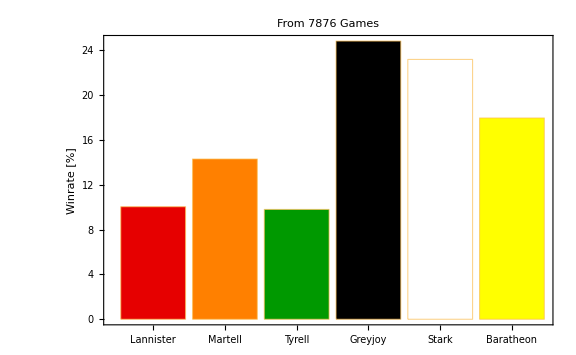
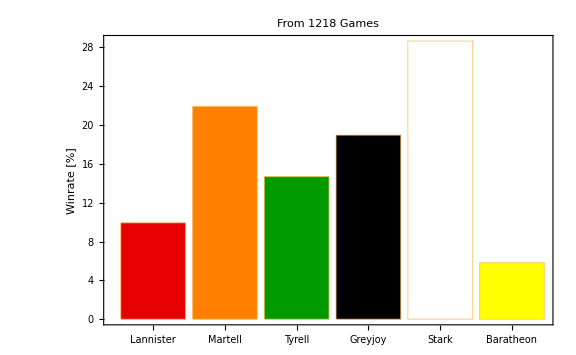
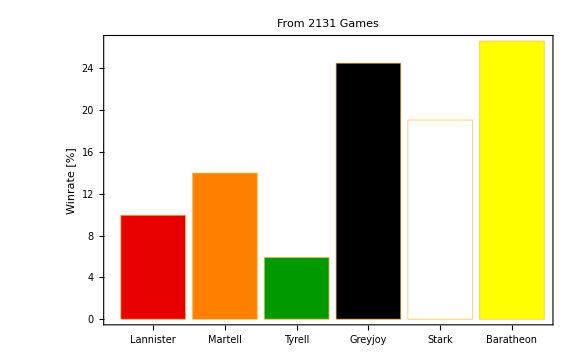
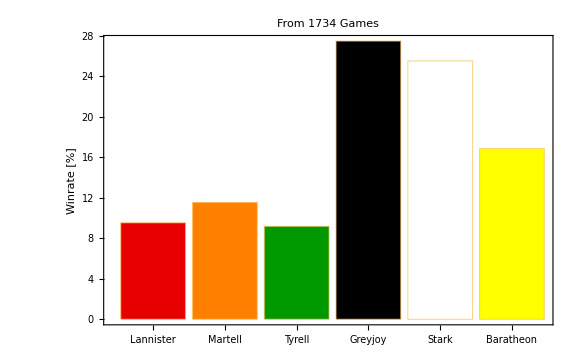

```mathematica
Row[{games2winners[nrs],games2winners[mb],games2winners[mt],games2winners[mbt]}]
```

```mathematica
Row[{games2castles[nrs],games2castles[mb],games2castles[mt],games2castles[mbt]}]
```

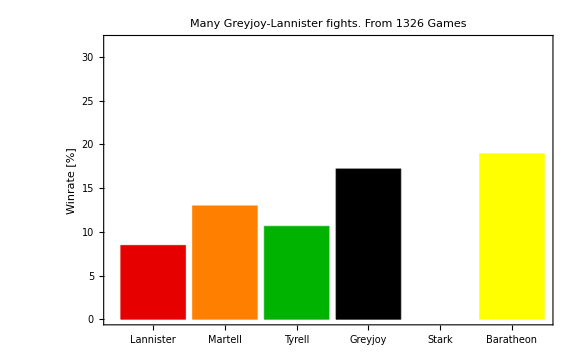

```mathematica
games2winners[allys[8,2],"Many Greyjoy-Lannister fights. "]
```

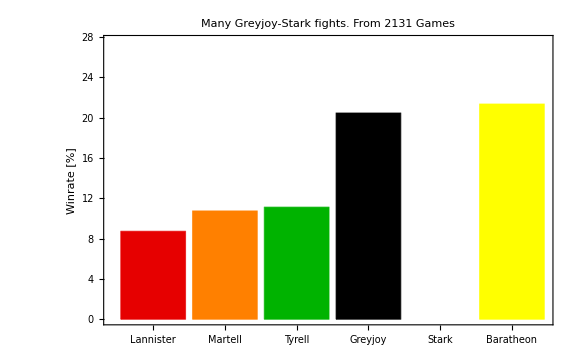

```mathematica
games2winners[allys[4,2],"Many Greyjoy-Stark fights. "]
```

```mathematica
allyl[5,1]
```

{}

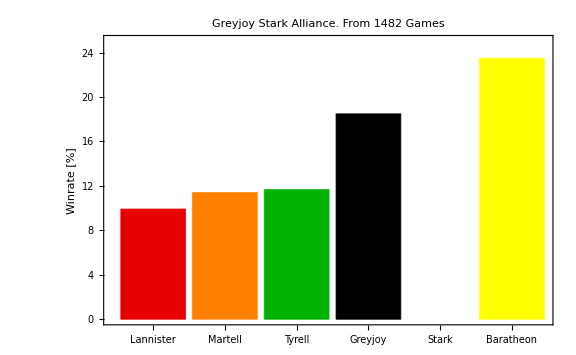

```mathematica
games2winners[allys[4,1],"Greyjoy Stark Alliance. "]
```

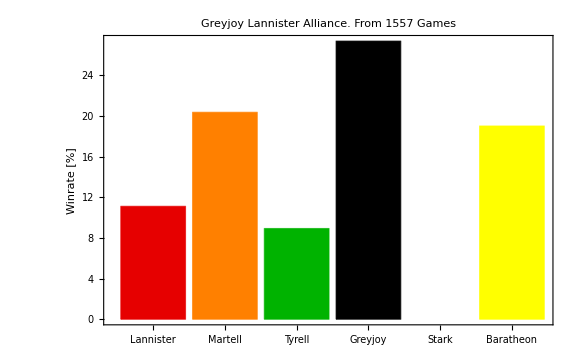

```mathematica
games2winners[allyl[4,2],"Greyjoy Lannister Alliance. "]
```

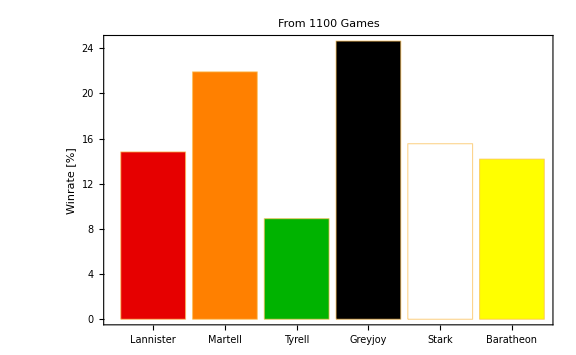
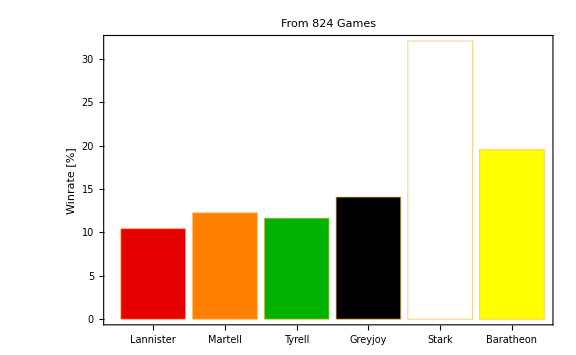
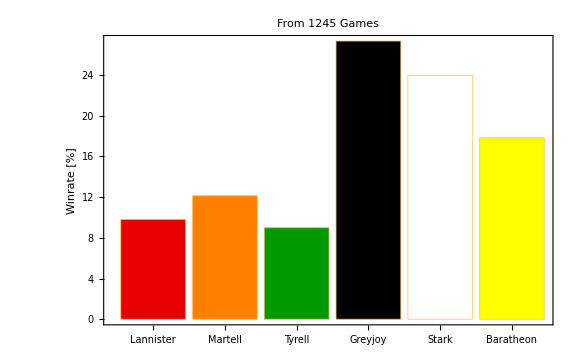
-Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{games2winners[nrs],games2winners[gs],games2winners[gl],games2winners[gsl]}]
```

```mathematica
gs//Length
```

1927

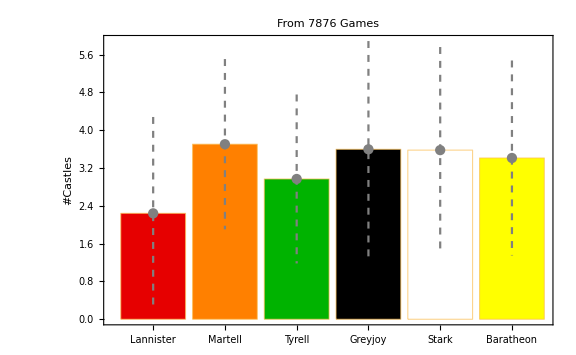
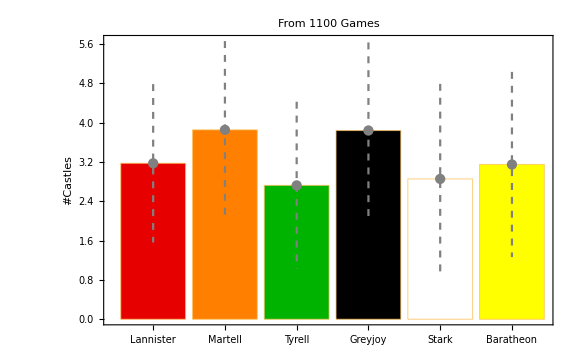
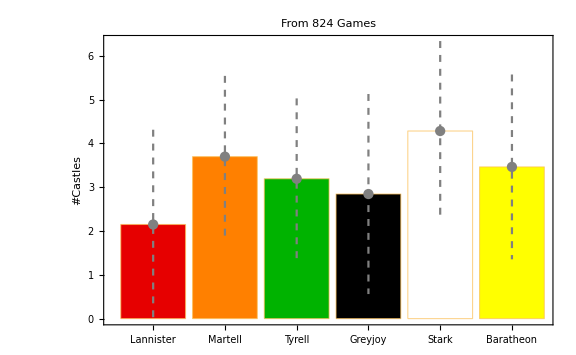
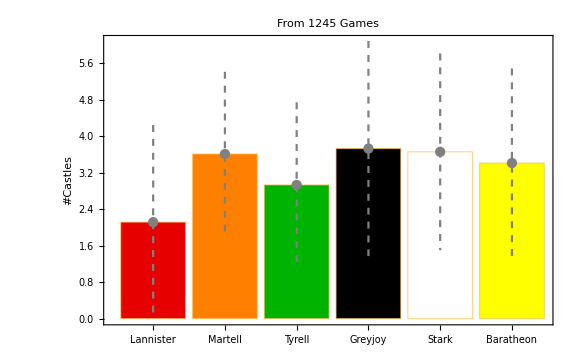

```mathematica
Row[{games2castles[nrs],games2castles[gs],games2castles[gl],games2castles[gsl]}]
```

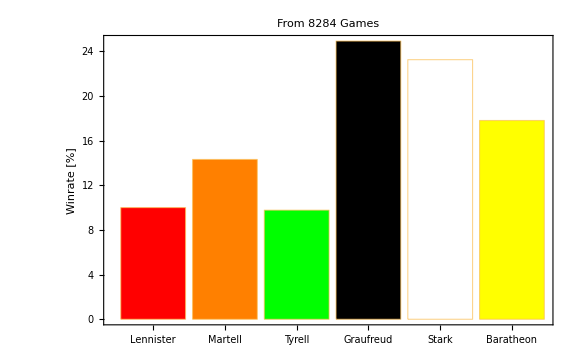
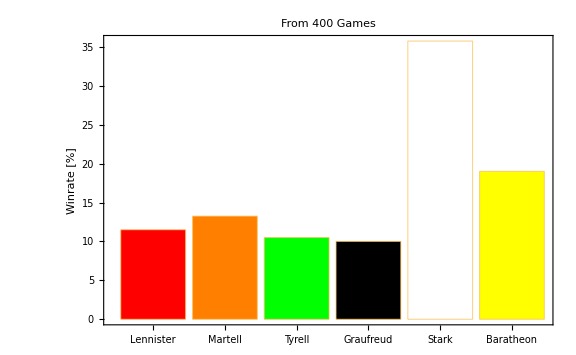

```mathematica
Row[{pos2winners[;;],games2winners[gl]}]
```

```mathematica
Transpose[{Transpose[GL][[2]],Transpose[GL][[2]]}]
```

{{5,5},{7,7},{5,5},{4,4},{4,4},{7,7},{4,4},{1,1},{4,4},{1,1},{4,4},{12,12},{10,10},{4,4},{5,5},{11,11},{8,8},{8,8},{4,4},{6,6},{9,9},{13,13},{9,9},{4,4},{4,4},{1,1},{7,7},{6,6},{5,5},{7,7},{1,1},{10,10},{11,11},{7,7},{9,9},{2,2},{8,8},{11,11},{13,13},{0,0},{5,5},{6,6},{7,7},{1,1},{5,5},{9,9},{8,8},{9,9},{3,3},{2,2},{2,2},{12,12},{4,4},{0,0},{7,7},{2,2},{7,7},{3,3},{3,3},{3,3},{1,1},{5,5},{8,8},{5,5},{11,11},{9,9},{0,0},{4,4},{4,4},{2,2},{4,4},{9,9},{12,12},{6,6},{13,13},2959,{10,10},{8,8},{0,0},{6,6},{8,8},{9,9},{3,3},{9,9},{5,5},{3,3},{1,1},{1,1},{7,7},{1,1},{5,5},{7,7},{1,1},{4,4},{5,5},{12,12},{0,0},{4,4},{9,9},{4,4},{0,0},{3,3},{9,9},{5,5},{9,9},{8,8},{1,1},{3,3},{10,10},{7,7},{9,9},{4,4},{6,6},{5,5},{6,6},{8,8},{9,9},{4,4},{5,5},{11,11},{0,0},{6,6},{5,5},{1,1},{6,6},{5,5},{7,7},{7,7},{0,0},{2,2},{6,6},{9,9},{7,7},{7,7},{7,7},{8,8},{5,5},{9,9},{6,6},{4,4},{3,3},{3,3},{4,4},{5,5},{8,8},{3,3},{3,3},{4,4},{8,8},{4,4},{5,5}}
 |  |  |  |

```mathematica
{Transpose[GL][[2]],Transpose[GS][[2]]}
```

```mathematica
TakeLargest[GJfightshist]
```

TakeLargest[{{5,5},{7,2},{5,2},{4,3},{4,11},{7,3},{4,0},{1,3},{4,2},{1,1},{4,5},{12,1},{10,6},{4,1},{5,3},{11,2},{8,2},{8,1},{4,4},{6,3},{9,10},{13,11},{9,0},{4,0},{4,2},{1,6},{7,8},{6,0},{5,3},{7,0},{1,14},{10,5},{11,14},{7,3},{9,7},{2,16},{8,10},{11,4},{13,4},{0,8},{5,14},{6,3},{7,3},{1,18},{5,2},{9,4},{8,2},{9,6},{3,6},{2,0},{2,9},{12,4},{4,13},{0,11},{7,12},{2,7},{7,2},{3,1},{3,3},{3,5},{1,5},{5,1},{8,0},{5,14},{11,1},{9,3},{0,6},{4,4},{4,1},{2,9},{4,4},{9,14},7732,{10,3},{2,17},{10,2},{12,3},{3,11},{6,4},{5,7},{7,0},{8,0},{6,3},{7,9},{9,0},{16,2},{0,3},{8,2},{8,1},{10,1},{6,1},{7,0},{7,4},{5,12},{3,11},{11,4},{6,9},{5,1},{8,3},{3,3},{6,7},{7,7},{5,1},{13,2},{10,3},{3,5},{3,3},{6,1},{5,3},{7,2},{0,5},{5,10},{5,1},{13,13},{10,7},{9,1},{4,6},{2,0},{4,2},{1,7},{3,0},{6,7},{4,9},{0,6},{1,3},{4,12},{8,1},{2,3},{0,4},{2,6},{5,1},{12,4},{7,10},{5,21},{5,2},{5,11},{5,1},{6,14},{2,8},{8,1},{8,1},{1,8},{13,1},{10,6},{0,5}}]
 |  |  |  |

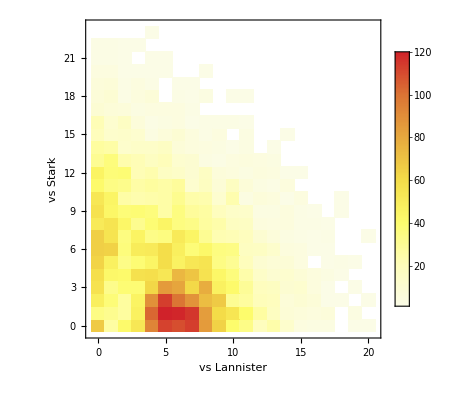

```mathematica
GJfightshist=Transpose[{Transpose[GL][[2]],Transpose[GS][[2]]}];
DensityHistogram[GJfightshist,FrameLabel->{"vs Lannister","vs Stark"},ColorFunction->(ColorData["Temperature"][Rescale[#1,{-120,120}]]&),ChartLegends->Automatic,ColorFunctionScaling->False]
```

```mathematica
Histogram3D[Transpose[{Transpose[GL][[2]],Transpose[GS][[2]]}],AxesLabel->{"vs Lannister","vs Stark","# of Games"}]
```

-Graphics3D-

```mathematica
For[i=150,i≤250,i++,If[splitted[[i,1,1]]!=nrs[[i]],Print[splitted[[i,1,1]]," and ",nrs[[i]]];,Print["same"]];]
```

```mathematica
Table[If[splitted[[i,1,1]]==nrs[[i]],Print[splitted[[i,1,1]]],Print["same"]],{i,1,Length[splitted]}]
```

{Null,3107,If[111431=={90001,90017,90028,90032,90035,90051,90070,90078,90079,90083,90087,90089,90091,90092,90093,90113,90116,90132,90142,90144,90149,90154,90155,90162,90171,90174,90175,90192,90204,90206,90209,90212,90213,90219,90223,90224,90230,90236,90247,90252,90254,90256,90258,90260,90275,90279,90280,90290,90294,90299,90320,90322,90329,90335,90350,90352,90359,90368,90386,90388,90401,90403,90407,90410,90416,90417,90423,2968,111036,111052,111057,111067,111088,111089,111103,111113,111122,111124,111131,111133,111137,111140,111142,111147,111149,111152,111156,111171,111172,111174,111177,111184,111187,111189,111193,111206,111209,111219,111237,111239,111245,111257,111264,111268,111273,111274,111282,111315,111323,111330,111332,111333,111336,111340,111343,111353,111358,111362,111365,111369,111371,111377,111382,111385,111398,111399,111401,111404,111406,111408,111409,111411,111414,111425,111431}⟦3109⟧,1,Print[same]]}
 |  |  |  |

Get 1 if Greyjoy fights more then 2 against a side and less then 2 against the other:

```mathematica
a=If[#<2,1,0]&/@Transpose[GL][[2]];
```

```mathematica
b=If[#>2,1,0]&/@Transpose[GS][[2]];
```

```mathematica
Length[nrs[[Position[allianceGS,1]//Flatten]]]
```

2678

```mathematica
allianceGL=(If[#>3,1,0]&/@Transpose[GS][[2]])*(If[#<4,1,0]&/@Transpose[GL][[2]]);
allianceGS=(If[#>3,1,0]&/@Transpose[GL][[2]])*(If[#<4,1,0]&/@Transpose[GS][[2]]);
```

```mathematica
Length[allianceGL]
```

7876

```mathematica
positionsGLalliance=Position[allianceGL,1]//Flatten;
positionsGSalliance=Position[allianceGS,1]//Flatten;
```

```mathematica
nrs[[positionsGLalliance]]
```

{90174,90209,90224,90252,90260,90294,90320,90335,90352,90388,90401,90423,90444,90487,90498,90573,90580,90681,90696,90697,90703,90725,90739,90748,90788,90826,90857,90861,90879,90914,90939,90969,90977,90987,90995,90998,91050,91076,91139,91210,91218,91228,91245,91261,91314,91317,91329,91342,91361,91377,91387,91417,91438,91450,91478,91480,91487,91516,91549,91562,91600,91621,91647,91654,91682,91688,91705,91740,91748,91762,91793,91852,91884,91922,91946,92039,92071,92095,92111,92136,92188,92284,92291,92303,92306,92331,92332,92336,92349,92379,92460,92475,92549,92595,92625,92641,92673,92746,92751,92765,92805,92839,92865,92899,92916,92920,92952,93001,93040,93059,93085,93094,93102,93103,93137,93186,93203,93228,93236,93250,93256,93282,93307,93341,93355,93474,93484,93531,93537,93556,93557,93573,93593,93600,93633,93657,93679,93685,93690,93693,93706,93707,93722,93739,93784,93813,93840,93920,93926,93951,93963,93968,93978,93987,93991,94053,94088,94118,94148,94157,94201,94218,94233,94257,94273,94368,94381,94394,94452,94514,94522,94526,94585,94689,94704,94708,94771,94786,94836,94842,94843,94875,94883,94914,95011,95085,95119,95144,95233,95271,95282,95288,95349,95403,95410,95431,95470,95529,95576,95611,95645,95674,95703,95769,95785,95828,95870,95919,96035,96113,96156,96167,96221,96274,96275,96298,96312,96317,96367,96383,96393,96394,96396,96400,96451,96455,96465,96491,96496,96573,96584,96596,96607,96611,96662,96727,96763,96779,96793,96821,96844,96877,96901,96935,96942,96951,96963,97002,97004,97006,97033,97074,97076,97098,97128,97151,97162,97172,97201,97216,97227,97271,97276,97316,97357,97394,97403,97416,97449,97452,97481,97485,97571,97718,97741,97858,97880,97886,97925,97984,98004,98075,98087,98125,98168,98204,98225,98237,98320,98336,98416,98488,98518,98552,98558,98606,98611,98619,98623,98652,98674,98782,98854,98958,98969,98970,98974,99030,99117,99204,99219,99259,99265,99332,99369,99422,99432,99459,99464,99465,99486,99536,99542,99546,99594,99609,99620,99624,99649,99663,99692,99696,99706,99723,99761,99790,99808,99845,99911,99931,99980,99987,100026,100033,100087,100094,100109,100120,100182,100213,100239,100290,100295,100357,100373,100384,100390,100399,100401,100417,100504,100507,100519,100528,100541,100568,100595,100599,100602,100612,100620,100635,100656,100662,100672,100678,100680,100692,100765,100786,100820,100848,100858,100884,100889,100943,100975,100978,100999,101015,101023,101036,101043,101055,101114,101142,101177,101221,101229,101250,101316,101327,101355,101447,101451,101465,101470,101481,101511,101534,101549,101568,101585,101587,101593,101607,101626,101660,101686,101766,101783,101790,101798,101842,101891,101914,101957,101968,101970,102001,102013,102032,102041,102056,102143,102145,102234,102249,102256,102288,102332,102337,102346,102376,102424,102435,102520,102545,102563,102580,102601,102639,102679,102698,102754,102755,102760,102767,102822,102826,102853,102864,102884,102885,102895,102897,102900,102940,103032,103101,103106,103135,103141,103173,103201,103231,103250,103305,103307,103345,103348,103349,103352,103361,103432,103471,103482,103522,103555,103604,103628,103661,103671,103672,103697,103718,103727,103745,103776,103778,103789,103790,103848,103876,103928,103946,103969,103988,104002,104042,104048,104050,104102,104144,104177,104183,104188,104208,104237,104264,104301,104320,104357,104433,104447,104460,104489,104549,104608,104610,104615,104650,104655,104661,104672,104704,104739,104777,104782,104796,104820,104842,104848,104854,104861,104866,104964,104986,104994,105003,105013,105098,105190,105305,105310,105311,105370,105372,105378,105392,105441,105444,105447,105477,105480,105491,105530,105572,105627,105635,105645,105666,105683,105684,105732,105739,105746,105781,105830,105890,105970,106067,106119,106160,106167,106170,106187,106323,106347,106359,106361,106370,106377,106390,106416,106457,106463,106475,106489,106493,106530,106544,106580,106589,106613,106657,106690,106751,106765,106770,106774,106803,106805,106809,106816,106871,106883,106889,106902,106903,106918,106923,106955,107041,107066,107095,107146,107205,107233,107260,107277,107293,107316,107336,107351,107356,107383,107431,107436,107437,107447,107496,107503,107536,107575,107626,107642,107656,107704,107758,107778,107782,107787,107793,107801,107810,107862,107912,107942,107951,107973,107986,108030,108102,108117,108152,108204,108217,108229,108295,108374,108389,108403,108435,108459,108561,108573,108578,108617,108625,108645,108650,108729,108784,108785,108833,108876,108901,108974,109073,109076,109100,109175,109219,109264,109284,109305,109354,109380,109393,109421,109425,109442,109466,109470,109498,109508,109534,109559,109638,109649,109707,109842,109933,109935,109946,109947,109961,109988,109997,110060,110071,110074,110118,110292,110311,110379,110427,110450,110454,110510,110543,110599,110603,110631,110740,110757,110763,110774,110840,110843,110844,110846,110871,110881,110903,111011,111034,111052,111057,111067,111137,111149,111152,111177,111184,111273,111315,111340,111399,111408,111409,111446,111499,111507,111512,111514,111524,111530,111621,111658,111712,111725,111747,111775,111808,111810,111939,111941,111988,111991,111998,112011,112028,112071,112092,112121,112163,112167,112174,112207,112219,112243,112253,112274,112277,112335,112384,112485,112519,112542,112651,112663,112677,112703,112747,112826,112889,112913,112946,112969,112993,113000,113092,113108,113148,113215,113321,113378,113455,113524,113527,113545,113547,113596,113600,113602,113603,113632,113689,113692,113726,113773,113781,113842,113871,113883,113886,113926,113946,113986,113990,114016,114035,114050,114091,114097,114126,114170,114178,114179,114188,114209,114222,114231,114256,114258,114286,114295,114343,114395,114400,114412,114432,114439,114549,114607,114639,114668,114689,114692,114713,114750,114810,114817,114829,114837,114954,115022,115042,115049,115191,115223,115224,115225,115238,115264,115289,115354,115372,115378,115386,115389,115464,115466,115476,115487,115530,115558,115563,115570,115726,115740,115761,115808,115834,115841,115852,115899,115913,116002,116013,116098,116124,116128,116137,116138,116144,116152,116222,116235,116256,116259,116263,116272,116331,116342,116409,116416,116449,116468,116534,116538,116560,116640,116669,116705,116728,116742,116747,116767,116802,116817,116827,116835,116855,116865,116878,116915,116952,116957,116972,116979,117002,117007,117060,117068,117081,117096,117102,117103,117136,117157,117236,117266,117317,117340,117367,117399,117412,117480,117494,117549,117582,117622,117644,117699,117700,117758,117797,117833,117855,117864,117886,117919,117943,117978,118090,118101,118125,118152,118155,118234,118267,118273,118301,118321,118324,118343,118384,118430,118452,118471,118525,118577,118581,118604,118630,118640,118658,118713,118717,118718,118833,118843,118876,118952,118956,118990,119012,119018,119026,119059,119075,119088,119091,119182,119196,119209,119218,119222,119236,119242,119336,119343,119344,119356,119362,119404,119418,119425,119467,119475,119503,119555,119564,119593,119630,119642,119648,119694,119706,119712,119769,119775,119780,119801,119844,119860,119879,119886,119896,119924,119930,119965,120004,120113,120123,120131,120143,120163,120186,120220,120221,120230,120295,120313,120359,120387,120391,120399,120410,120424,120451,120462,120559,120577,120637,120645,120697,120788,120805,120869,120892,120910,120918,120989,121026,121048,121082,121121,121129,121188,121192,121228,121247,121251,121258,121300,121359,121369,121383,121425,121512,121523,121535,121658,121715,121749,121760,121773,121838,121858,121947,121968,121970,121981,122030,122046,122051,122128,122149,122153,122203,122218,122253,122286,122338,122374,122428,122454,122459,122465,122467,122505,122525,122598,122695,122719,122729,122735,122738,122740,122765,122769,122784,122820,122846,122906,122910,122921,122922,122959,122993,122997,123057,123178,123182,123190,123294,123315,123334,123400,123406,123407,123417,123451,123501,123562,123600,123602,123603,123651,123712,123726,123750,123813,123814,123816,123817,123877,123884,123914,123930,123961,123989,123998,124015,124032,124040,124042,124055,124061,124063,124081,124121,124161,124181,124183,124200,124240,124323,124352,124353,124397,124399,124464,124466,124467,124477,124498,124524,124557,124593,124610,124643,124693,124705,124768,124795,124824,124876,124881,124890,124892,124895,125073,125084,125118,125133,125166,125222,125231,125269,125307,125380,125416,125418,125456,125481,125491,125500,125533,125555,125593,125598,125609,125619,125622,125625,125627,125631,125661,125667,125668,125670,125677,125710,125748,125754,125755,125758,125760,125762,125810,125872,125943,125965,125975,125987,125993,126003,126048,126049,126050,126053,126119,126141,126149,126154,126169,126227,126292,126321,126355,126368,126422,126443,126496,126498,126532,126533,126538,126552,126597,126603,126616,126630,126651,126689,126704,126723,126731,126743,126754,126762,126774,126790,126832,126838,126843,126847,126857,126922,126946,126978,127065,127137,127153,127235,127307,127363,127411,127447,127453,127454,127455,127456,127462,127466,127478,127485,127609,127659,127719,127731,127792,127822,127839,127843,127856,127864,127868,127896,127961,127994,128074,128084,128100,128157,128158,128163,128167,128270,128293,128294,128314,128319,128324,128331,128385,128391,128415,128421,128422,128423,128428,128440,128485,128488,128497,128538,128542,128547,128549,128558,128562,128573,128576,128595,128606,128656,128659,128677,128700,128704,128710,128777,128797,128839,128875,128877,128908,128930,128934,128984,129000,129020,129039,129088,129091,129149,129229,129309,129359,129376,129377,129406,129438,129617,129646,129817,129865,129892,129896,129920,129934,129936,129952,129997,130000,130002,130026,130057,130060,130111,130133,130138,130164,130170,130186,130237,130279,130340,130350,130425,130490,130500,130533,130566,130608,130612,130613,130700,130728,130743,130748,130763,130793,130848,130869,130872,130875,130940,130953,130955,130974,131077,131109,131129,131143,131151,131170,131201,131241,131261,131302,131312,131321,131322,131323,131368,131375,131389,131390,131404,131418,131501,131522,131540,131630,131648,131698,131738,131744,131785,131790,131850,131851,131870,131885,131896,131940,131984,131986,131999,132001,132052,132059,132066,132070,132103,132108,132109,132131,132133,132158,132159,132168,132203,132208,132235,132346,132350,132433,132458,132461,132544,132555,132638,132649,132658,132671,132715,132721,132737,132741,132745,132825,132834,132841,132846,132851,132879,132887,132909,132925,132959,132988,133035,133055,133064,133088,133100,133106,133121,133143,133147,133207,133224,133230,133251,133266,133272,133308,133378,133401,133421,133482,133508,133525,133545,133575,133622,133623,133637,133698,133708,133761,133864,133872,133873,133900,133911,133958,133976,134026,134086,134104,134124,134152,134197,134202,134220,134223,134265,134275,134282,134330,134375,134401,134447,134456,134468,134512,134557,134592,134597,134647,134653,134667,134670,134691,134759,134773,134835,134909,134938,134977,134978,135006,135105,135122,135204,135219,135235,135297,135304,135340,135349,135444,135453,135489,135497,135518,135535,135561,135588,135633,135646,135681,135685,135726,135785,135803,135833,135852,135863,135920,135954,135976,135982,135995,135998,136045,136048,136051,136067,136099,136107,136116,136231,136242,136246,136263,136265,136270,136285,136320,136369,136493,136514,136519,136627,136647,136714,136770,136781,136785,136792,136816,136824,136907,136914,136963,137008,137029,137083,137126,137130,137155,137169,137211,137246,137269,137283,137389,137438,137452,137491,137501,137502,137516,137525,137527,137598,137605,137614,137649,137666,137667,137683,137715,137725,137734,137761,137881,137983,138005,138011,138028,138056,138073,138129,138232,138329,138458,138465,138519,138524,138529,138571,138592,138608,138609,138624,138648,138649,138673,138693,138734,138803,138840,138863,138866,138904,138928,138958,138993,138999,139003,139007,139022,139027,139031,139113,139124,139145,139163,139198,139202,139244,139259,139290,139299,139306,139345,139366,139395,139407,139429,139460,139505,139619,139644,139686,139710,139712,139815,139869,139884,139923,139943,139971,139976,139983,139998,140027,140040,140097,140098,140101,140142,140147,140151,140168,140170,140231,140241,140246,140254,140274,140296,140379,140410,140442,140461,140518,140528,140539,140549,140577,140599,140753,140766,140773,140805,140832,140884,140892,140905,140916,140933,140943,141001,141019,141095,141107,141131,141202,141206,141238,141241,141272,141273,141350,141406,141420,141421,141521,141529,141544,141546,141558,141563,141580,141670,141706,141764,141774,141810,141829,141886,141932,142001,142027,142033,142038,142054,142114,142132,142155,142171,142182,142183,142212,142229,142264,142275,142293,142324,142354,142357,142386,142422,142474,142498,142528,142550,142583,142594,142688,142788,142814,142821,142850,142852,142859,142860,142865,142866,142881,142885,142929,142995,142996,143009,143023,143109,143118,143138,143242,143256,143335,143372,143415,143417,143425,143462,143465,143466,143495,143518,143529,143555,143601,143639,143650,143745,143750,143757,143784,143839,143863,143870,143902,143950,143955,144005,144036,144068,144163,144176,144196,144200,144203,144209,144229,144244,144255,144267,144369,144434,144470,144560,144596,144627,144673,144736,144778,144808}

```mathematica
allianceGL*allianceGS
```

```mathematica
nrs[[Position[allianceGL*allianceGS,1]//Flatten]]
```

{}